## Images

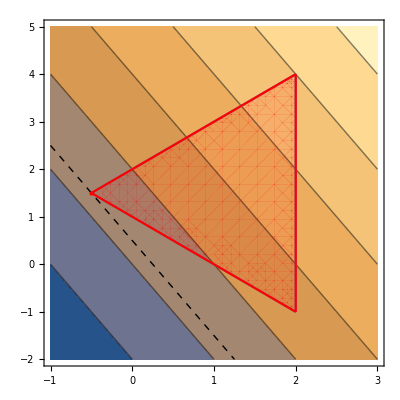

```mathematica
Show[ContourPlot[2 x+y,{x,-1,3},{y,-2, 5}],Show[RegionPlot[-x≥-2&&x+y≥1&&x-y≥-2,{x,-1,3},{y,-2,5},PlotStyle->{Opacity[.1],Red}],ParametricPlot[{ t,1- t},{t,-.5,2},PlotStyle->{Red}],ParametricPlot[{ t,2+t},{t,-.5,2},PlotStyle->{Red}],ParametricPlot[{ 2,t},{t,-1,4},PlotStyle->{Red}]],ContourPlot[2x+ y==1/2,{x,-1,3},{y,-2, 5},ContourStyle->{Black,Thick,Dashed}],Graphics[{PointSize[Large],Red,Point[{-0.5,3/2}]}]]
```

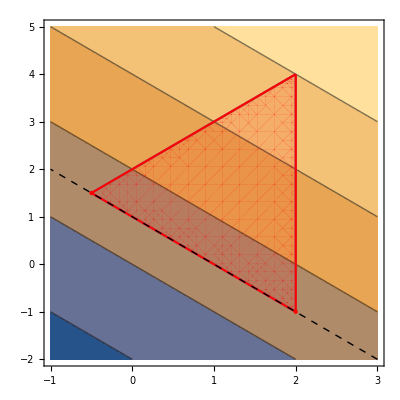

```mathematica
Show[ContourPlot[ x+y,{x,-1,3},{y,-2, 5}],Show[RegionPlot[-x≥-2&&x+y≥1&&x-y≥-2,{x,-1,3},{y,-2,5},PlotStyle->{Opacity[.1],Red}],ParametricPlot[{ t,1- t},{t,-.5,2},PlotStyle->{Red}],ParametricPlot[{ t,2+t},{t,-.5,2},PlotStyle->{Red}],ParametricPlot[{ 2,t},{t,-1,4},PlotStyle->{Red}]],ContourPlot[x+ y==1,{x,-1,3},{y,-2, 5},ContourStyle->{Black,Thick,Dashed}],Graphics[{PointSize[Large],Red,Point[{{-0.5,3/2},{2,-1}}]}]]
```

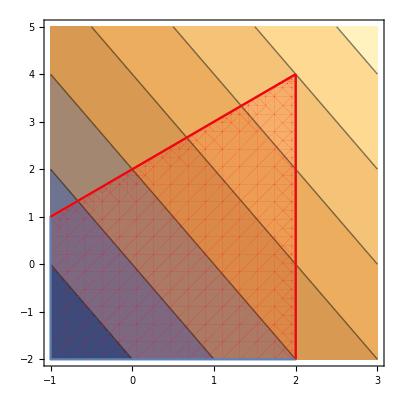

```mathematica
Show[ContourPlot[2x+ y,{x,-1,3},{y,-2, 5}],Show[RegionPlot[-x≥-2&&x-y≥-2,{x,-1,3},{y,-2,5},PlotStyle->{Opacity[.1],Red}],ParametricPlot[{ t,2+t},{t,-1,2},PlotStyle->{Red}],ParametricPlot[{ 2,t},{t,-2,4},PlotStyle->{Red}]]]
```

## Linear Programming

```mathematica
Manipulate[Show[ContourPlot[a x+b y,{x,-1,3},{y,-2, 5}],constraints,ContourPlot[a x+b y==If[a≥Abs[b],-a/2+3 b/2,2 a-b],{x,-1,3},{y,-2, 5},ContourStyle->{Black,Thick,Dashed}],Which[a>b,Graphics[{PointSize[Large],Red,Point[{-0.5,3/2}]}],a==b,Graphics[{PointSize[Large],Red,Point[{{-0.5,3/2},{2,-1}}]}],a<b,Graphics[{PointSize[Large],Red,Point[{2,-1}]}]]],{{a,2},-10,10},{{b,1},0,10},Initialization:>(constraints=Show[RegionPlot[-x≥-2&&x+y≥1&&x-y≥-2,{x,-1,3},{y,-2,5},PlotStyle->{Opacity[.1],Red}],ParametricPlot[{ t,1- t},{t,-.5,2},PlotStyle->{Red}],ParametricPlot[{ t,2+t},{t,-.5,2},PlotStyle->{Red}],ParametricPlot[{ 2,t},{t,-1,4},PlotStyle->{Red}]];)]
```

## Unbounded Region

```mathematica
Manipulate[Show[ContourPlot[a x+b y,{x,-1,3},{y,-2, 5}],uconstraints],{{a,2},-10,10},{{b,1},-10,10},Initialization:>(uconstraints=Show[RegionPlot[-x≥-2&&x-y≥-2,{x,-1,3},{y,-2,5},PlotStyle->{Opacity[.1],Red}],ParametricPlot[{ t,2+t},{t,-1,2},PlotStyle->{Red}],ParametricPlot[{ 2,t},{t,-2,4},PlotStyle->{Red}]];)]
```